# Report Project 1

Course code: IX1500
Date: 2024-09-16

Neo Gullberg, neog@kth.se

Task 1: The Path of a Particle

## Summary

### Task

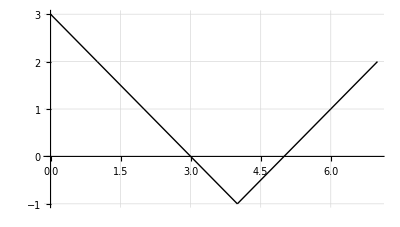
A partical moves in a the xy plane according to the following moves:
U:(m, n) → (m + 1, n + 1)
L:(m, n) → (m + 1, n − 1)
where m and n are both integers. For example see the following Figure.
-Graphics-
a) How many such paths are there from (0, 3) to (7, 2)? Explain and print all such paths.
b) How many paths from (0, 3) to (7, 2) touch or cross x-axis at least once? Explain and print all such paths.
c) How many paths from (0, 3) to (7, 2) never touch or cross x-axis? Explain and print all such paths.
d) How many paths from (7, 6) to (20, 5) never touch or cross x-axis? Explain your solution.

### Result

a)   35 paths.
b)    7 paths.
b)   28 paths.
b) 1703 paths.
The full list of paths for each sub-task can be seen in their corresponding data files (.dat) which should be generated in a folder labeled data after running the python program.

### Solution

#### a)

Each move takes us one step closer, along the x-axis, to our destination.
Since we have to travel 7 steps along the positive x-axis, it means we have 7 moves to make where we can either go up or down.
With those 7 moves we have to, in total, move -1 steps along the y-axis.
This means we have to make 1 more down (L) move than up (U) move.
Now the problem turns into: How many ways can we arrange the letters LLLLUUU?
This is straightforward to calculate:
(7!)/(4!×3!)=(7×6×5)/6=7×5=35
Therefore, 35 paths is our answer.

#### b)

Now we have to consider if the path ever touches or crosses the x-axis.
The earliest possible touch is calculated by taking the start point (0, 3) and only performing down moves until y=0.
This means we have to perform 3 down moves, which results in the earliest touch being at (3, 0).
To calculate the latest possible touch we use the same principle, but backwards.
We start at (7, 2) and go down to the left until we hit the x-axis, which results in the latest touch being at (5, 0).
It is impossible for us to ever hit (4, 0) since there are no arrangements of 4 moves that moves us -3 steps along the y-axis.
This means we have to account for 3 scenarios: only touching (3, 0), only touching (5, 0), or touching both.
To calculate this we can calculate the possible ways to hit (3, 0), add that with the possible ways to hit (5, 0),
and lastly subtract the sum by the amount of times we hit both.

Ways to hit (3, 0):
The first 3 moves will always be LLL. So the question turns into: How many ways can we arrange the 4 letters LUUU (LLLLUUU)?
(4!)/(3!) = 4

Ways to hit (5, 0):
The last 2 moves will always be UU. So the question turns into: How many ways can we arrange the 5 letters LLLLU (LLLLUUU)?
(5!)/(4!) = 5

Ways to hit (3, 0) and (5, 0):
This means we have to go from (3, 0) to (5, 0) which turns into the problem: How many ways can we arrange the 2 letters LU (LLLLUUU)?
2! = 2

If we add all of this together we get the following:
4+5-2=9-2=7
Therefore, 7 paths is our answer.

#### c)

This is the opposite of what we calculated in the previous sub-task.
Since that is the case, in addition to calculating the total number of paths from (0, 3) to (7, 2) in the first sub-task,
we can take the result from the first calculation (a) and subtract the result from the second calculation (b) to give us our answer.
35-7=28
Therefore, 28 paths is our answer.

#### d)

This is like a combination of all three prior sub-tasks.
The first step is calculating the total number of paths from (7, 6) to (20, 5).
We have 13 moves in total to take us -1 step along the y-axis.
This once again means we have to have one more L than U.
The number of L’s is 7, and the number of U’s is 6.
The total is therefore calculated by asking: How many ways can we arrange the letters LLLLLLLUUUUUU?
(13!)/(7!×6!)=(13×12×11×10×9×8)/(6×5×4×3×2)=13×2×11×3×2=1716
Therefore, the total number of paths from (7, 6) to (20, 5) is 1716.

Now we have to calculate the number of paths that touch or cross the x-axis.
The first possible touch is: (7,6)+6(1,-1)=(13,0)
The last possible touch is: (20,5)+5(-1,-1)=(15,0)
Similar to last time, the point (14, 0) is impossible to reach since there is no way to take -6 steps along the y-axis in 7 moves.

Ways to hit (13, 0):
The first 6 moves will always be LLLLLL. So the question turns into: How many ways can we arrange the 7 letters LUUUUUU (LLLLLLLUUUUUU)?
(7!)/(6!) = 7

Ways to hit (15, 0):
The last 5 moves will always be UUUUU. So the question turns into: How many ways can we arrange the 8 letters LLLLLLLU (LLLLLLLUUUUUU)?
(8!)/(7!) = 8

Ways to hit (13, 0) and (15, 0):
This means we have to go from (13, 0) to (15, 0) which turns into the problem: How many ways can we arrange the 2 letters LU (LLLLLLLUUUUUU)?
2! = 2

If we add all of this together we get the following:
7+8-2=15-2=13
Therefore, the number of paths from (7, 6) to (20, 5) that touch or cross the x-axis is 13.

Now with both previous results we can find the number of paths from (7, 6) to (20, 5) that never touch or cross the x-axis.
1716-13=1703
Therefore, 1703 paths is our answer.

## Formulas and Equations

The main formula used  throughout this task and all its sub-tasks is the following:
(n!)/(n_1!×n_2!×…×n_k!)
It is used to calculate the permutations of a given sequence, accounting for repetitions of certain items.
n is the total number of items to arrange, and n_1, n_2, …, n_k​ are the frequencies of the distinct items.
Principles of inclusion/exclusion were also applied to avoid counting identical paths more than once.

## Discussion

What I learned from this task is how to use combinatorics to solve simple problems concerning the path a particle can take. It gave me a deeper understanding of how certain conditions, such as crossing or not crossing a specific line, affect the number of possible solutions to a problem of this kind. I gained experience in calculating the solutions both by hand, and also by coding algorithms to count and print out all. Coding a solution was especially helpful in double checking that my results seemed correct. The reason I choose to generate my paths with Python instead of Mathematica is merely because I personally feel Python is much easier to work with, especially when it comes to writing functions. However, I will agree that visualizations are quite easy to create in Mathematica, and that is why I choose to combine the two. My takeaway from this task is to not always jump straight to coding a solution (at least when it comes to tasks like this). I was in fact able to come up with a solution using code, but I didn’t quite understand it in math terms. It wasn’t until I sat down and solved it with pen and paper that I felt I finally grasped the problem somewhat fully.

## Code

### Python

The Python programming language was used to generate all possible arrangements of paths for a given task.
All code can be found in ../python/task_1/code, and the generated arrangement data can be found in ../python/task_1/data (after running the program).
However, I will try to explain some of it here:

This function generates an array of all possible sequences for a given set of characters with the help of recursion. Each sequence that gets added to the array must fulfill the condition specified by the is_valid function. There is probably a better way  to write this, but it works.

def find_sequences(current, characters, depth, is_valid):
	found = []

	if is_valid(current):
		if depth <= 0:
			found.append(current)
		else:
			for c in characters:
				found += find_sequences(current + c, characters, depth - 1, is_valid)

	return found

Here is an example of an is_valid function which gets passed to find_sequences. This checks to see if a sequence follows the condition for the first sub-task. As explained in the solution, we have 7 moves to make of which 4 must be L and 3 must be U. If the count for those are ever larger than those values then the sequence is invalid and the function returns false.

def is_valid_a(sequence):
	# a) How many such paths are there from (0, 3) to (7, 2)?
	u_count = 0
	l_count = 0

	for c in sequence:
		match c:
			case 'U': u_count += 1
			case 'L': l_count += 1
		if u_count > 3 or l_count > 4:
			return False

	return True

### Wolfram

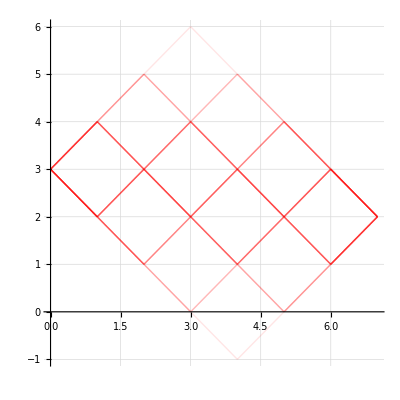

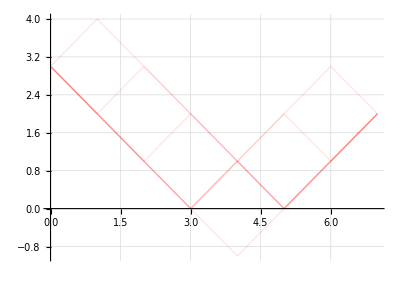

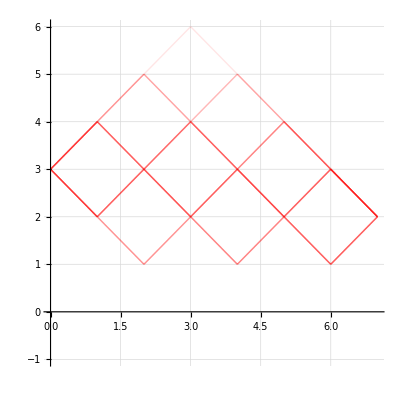

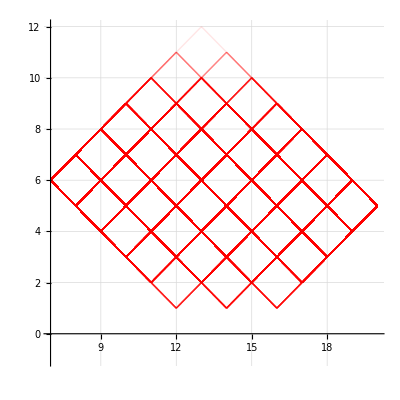

```mathematica
ClearAll["Global`*"];

createLines[sequenceString_,initialX_,initialY_]:=Module[
{lines,char,currentX,currentY,nextY},

lines = {};

currentX=initialX;
currentY=initialY;

For[i=1,i<=StringLength[sequenceString],i++,
char=StringPart[sequenceString,i];
nextY=currentY;
If[char=="L",nextY--];
If[char=="U",nextY++];
AppendTo[lines,Line[{{currentX,currentY},{currentX+1,nextY}}]];
currentX++;
currentY=nextY;
];

Return[lines];
];

graphSequence[sequenceString_,initialX_,initialY_,plotRange_]:=Module[
{},
graph=Graphics[
createLines[sequenceString,initialX,initialY],
plotRange,
Axes->True,
AxesOrigin->{initialX,0},
GridLines->Automatic
];
Return[graph];
];

graphMultipleSequences[sequenceStrings_,initialX_,initialY_,plotRange_]:=Module[
{allLines,sequenceString},
allLines={};
Do[
AppendTo[allLines,createLines[ToString[sequenceString],initialX,initialY]];
,
{sequenceString,sequenceStrings}
];
allLines=Style[allLines,Red,Opacity[0.1]]; (* color *)
Print[allLines];
graph=Graphics[
allLines,
plotRange,
Axes->True,
AxesOrigin->{initialX,0},
GridLines->Automatic
];
Return[graph];
];

readFileAsList[filepath_]:=ReadList[FileNameJoin[{NotebookDirectory[],filepath}]];

graphSequence["LLLLUUU",0,3,PlotRange->{{0,7},{-1,3}}]; (* just the example figure *)

sequenceStringsA=readFileAsList["../python/task_1/data/a.dat"];
sequenceStringsB=readFileAsList["../python/task_1/data/b.dat"];
sequenceStringsC=readFileAsList["../python/task_1/data/c.dat"];
sequenceStringsD=readFileAsList["../python/task_1/data/d.dat"];
graphMultipleSequences[sequenceStringsA,0,3,PlotRange->{{0,7},{-1,6}}]
graphMultipleSequences[sequenceStringsB,0,3,PlotRange->{{0,7},{-1,4}}]
graphMultipleSequences[sequenceStringsC,0,3,PlotRange->{{0,7},{-1,6}}]
graphMultipleSequences[sequenceStringsD,7,6,PlotRange->{{7,20},{-1,12}}]
```

Task 2: The Ways a Ballot Can Be Selected

## Summary

### Task

The candidates A and B are the finalist for an award.
A committee of 11 

members will place their vote (in favour of one of the candidates) into a ballot

box.
Suppose that A receives 9 votes and B receives 2.
In how many ways can the 

ballot be selected, one at a time, from the ballot box so that there are always more votes in favour of A.
Explain your solution.
Calculate the probability that 

A will be strictly ahead of B throughout the count.

### Result

I got that the number of ways that the ballot can be selected so that there are always more votes in favour of A is 35, for which the probability is roughly 64%.

### Solution

There are 11 votes in total, 9 for A and 2 for B.
Throughout the whole vote A has to have more votes than B.
This means the first two votes must go to A.
Then there is a split: either one goes to A or one goes to B.
The A case:
	Now that A has three votes B can never catch up.
	Therefore the problem turns into: How many ways can we arrange the letters AAAAAABB?
	(8!)/(6!×2!)=(8×7)/2=4×7=28
	For this case the number of arrangements are 28.
The B case:
	Now A has 2 votes and B has 1 vote.
	Therefore, the next vote must be for A since they can’t have equal votes.
	The sequence so far looks like AABA, and now B can never catch up.
	Therefore the problem turns into: How many ways can we arrange the letters AAAAAAB?
	(7!)/(6!×1!)=7
	For this case the number of arrangements are 7.
Now we add up the two cases and get the following:
28+7=35
Therefore, the number of ways the ballot can be selected so that more votes are always in favour of A is 35.
To calculate the probability of this happening we first need the total number of possible arrangements.
(11!)/(9!×2!)=(11×10)/2=11×5=55
Then we divide the number of elements in the set of outcomes where A is always strictly ahead of B, 35, with the total number of outcomes, 55.
35/55=7/11≈ 64%
Therefore, the probability of A always being ahead of B is 64%.

## Formulas and Equations

Like the first task, the main formula used  throughout this task is the following:
(n!)/(n_1!×n_2!×…×n_k!)

## Discussion

I had an easier time with this task compared to the first one. Firstly, because they are quite similar which meant I had a good grasp of what to do. Secondly, because this time I started by doing my solution by hand instead of going straight to the computer just because we were allowed to use one. The stuff I said about Python and Mathematica still hold true for this task aswell.

## Code

### Python

Like in the last task, the Python programming language was used to generate all possible arrangements of paths.
All code can be found in ../python/task_2/code, and the generated arrangement data can be found in ../python/task_2/data (after running the program).
However, I will try to explain some of it here:

Similar to the find_sequences function that was used in the last task, but I wanted to experiment with another way of generating the arrangements so I came up with this. The symbol_list contains a list of symbols which each contain a letter and the amount left of that letter. This removes the need to keep track of the depth like in the last implementation. Instead, this one just stops running once all symbols counts are down to 0.

def find_sequences(symbol_list, is_valid, current = ""):
	found = []

	if is_valid(current):
		for i in range(len(symbol_list)):
			symbol_list_copy = copy.deepcopy(symbol_list)
			symbol = symbol_list_copy[i]
			if (symbol.count > 0):
				symbol.count -= 1
				found += find_sequences(symbol_list_copy, is_valid, current + symbol.letter)
		if len(found) == 0:
			found.append(current)

	return found

This is what gets passed to find_sequences. It counts the number of A’s and B’s and only returns true if the number of A’s is greater than the number of B’s.

def valid_test(current):
	if len(current) == 0:
		return True
	a_count = 0
	b_count = 0
	for c in current:
		match c:
			case 'A': a_count += 1
			case 'B': b_count += 1
	return a_count > b_count

### Wolfram

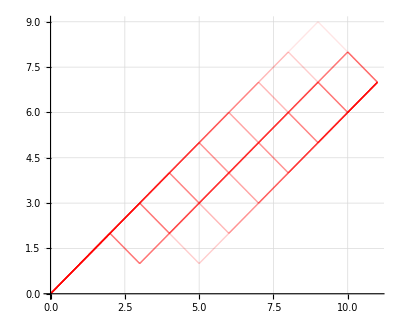

```mathematica
ClearAll["Global`*"];

createLines[sequenceString_,initialX_,initialY_]:=Module[
{lines,char,currentX,currentY,nextY},

lines = {};

currentX=initialX;
currentY=initialY;

For[i=1,i<=StringLength[sequenceString],i++,
char=StringPart[sequenceString,i];
nextY=currentY;
If[char=="B",nextY--];
If[char=="A",nextY++];
AppendTo[lines,Line[{{currentX,currentY},{currentX+1,nextY}}]];
currentX++;
currentY=nextY;
];

Return[lines];
];

graphSequence[sequenceString_,initialX_,initialY_,plotRange_]:=Module[
{},
graph=Graphics[
createLines[sequenceString,initialX,initialY],
plotRange,
Axes->True,
AxesOrigin->{initialX,0},
GridLines->Automatic
];
Return[graph];
];

graphMultipleSequences[sequenceStrings_,initialX_,initialY_,plotRange_]:=Module[
{allLines,sequenceString},
allLines={};
Do[
AppendTo[allLines,createLines[ToString[sequenceString],initialX,initialY]];
,
{sequenceString,sequenceStrings}
];
allLines=Style[allLines,Red,Opacity[0.1]]; (* color *)
Print[allLines];
graph=Graphics[
allLines,
plotRange,
Axes->True,
AxesOrigin->{initialX,0},
GridLines->Automatic
];
Return[graph];
];

readFileAsList[filepath_]:=ReadList[FileNameJoin[{NotebookDirectory[],filepath}]];

sequenceStrings=readFileAsList["../python/task_2/data/task.dat"];
graphMultipleSequences[sequenceStrings,0,0,PlotRange->{{0,11},{0,9}}]
```